```mathematica
Clear[x]
```

{0.,0.000172774,0.000690977,0.00155425,0.002762,0.00431339,0.00620734,0.00844256,0.0110175,0.0139303,0.0171791,0.0207616,0.0246753,0.0289174,0.0334851,0.0383752,0.0435844,0.049109,0.0549452,0.0610889,0.067536,0.074282,0.0813222,0.0886517,0.0962655,0.104158,0.112325,0.120759,0.129455,0.138408,0.14761,0.157056,0.166739,0.176652,0.186789,0.197142,0.207705,0.218469,0.229428,0.240574,0.2519,0.263396,0.275057,0.286873,0.298836,0.310938,0.32317,0.335525,0.347994,0.360568,0.373238,0.385995,0.398832,0.411738,0.424705,0.437725,0.450787,0.463883,0.477005,0.490142,0.503286,0.516428,0.529558,0.542668,0.555749,0.568791,0.581785,0.594723,0.607596,0.620394,0.633109,0.645732,0.658254,0.670667,0.682962,0.69513,0.707164,0.719054,0.730793,0.742373,0.753785,0.765022,0.776075,0.786938,0.797602,0.808061,0.818307,0.828333,0.838131,0.847697,0.857022,0.8661,0.874925,0.883491,0.891792,0.899823,0.907577,0.915049,0.922234,0.929128,0.935725,0.942021,0.948012,0.953693,0.95906,0.96411,0.968839,0.973245,0.977323,0.981071,0.984487,0.987568,0.990312,0.992718,0.994782,0.996505,0.997885,0.99892,0.999611,0.999957,0.999957,0.999611,0.99892,0.997885,0.996505,0.994782,0.992718,0.990312,0.987568,0.984487,0.981071,0.977323,0.973245,0.968839,0.96411,0.95906,0.953693,0.948012,0.942021,0.935725,0.929128,0.922234,0.915049,0.907577,0.899823,0.891792,0.883491,0.874925,0.8661,0.857022,0.847697,0.838131,0.828333,0.818307,0.808061,0.797602,0.786938,0.776075,0.765022,0.753785,0.742373,0.730793,0.719054,0.707164,0.69513,0.682962,0.670667,0.658254,0.645732,0.633109,0.620394,0.607596,0.594723,0.581785,0.568791,0.555749,0.542668,0.529558,0.516428,0.503286,0.490142,0.477005,0.463883,0.450787,0.437725,0.424705,0.411738,0.398832,0.385995,0.373238,0.360568,0.347994,0.335525,0.32317,0.310938,0.298836,0.286873,0.275057,0.263396,0.2519,0.240574,0.229428,0.218469,0.207705,0.197142,0.186789,0.176652,0.166739,0.157056,0.14761,0.138408,0.129455,0.120759,0.112325,0.104158,0.0962655,0.0886517,0.0813222,0.074282,0.067536,0.0610889,0.0549452,0.049109,0.0435844,0.0383752,0.0334851,0.0289174,0.0246753,0.0207616,0.0171791,0.0139303,0.0110175,0.00844256,0.00620734,0.00431339,0.002762,0.00155425,0.000690977,0.000172774,0.}

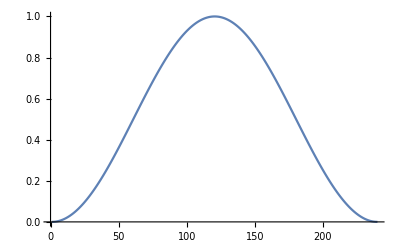

```mathematica
nPoints=240;
data = N@Table[Sin[x]^2,{x,0,Pi,Pi/(nPoints-1)}]
ListLinePlot[data]
```

```mathematica
(*subpowers*)
folderDriveName="C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new_Tom\\Sin4 intensity pulse\\"<>ToString[nPoints]<>" drive"
If[DirectoryQ[folderDriveName],None,CreateDirectory[folderDriveName]]
δ=10^-5;
Table[
Export[folderDriveName<>"\\sin4_"<>ToString[i]<>"_"<>ToString@Length@data<>".csv",N@Chop[{i/100 data},δ]],
{i,5,100,5}
]
```

240